FittedModel[0.247735-0.00106815 x+9.2684×10^-7 x^2]

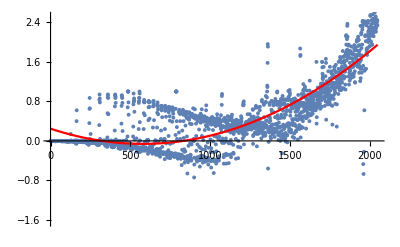

0.794276

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "min-fixed"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x+c*x^2,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```